```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["/Users/zackarywindham/Research/Post-Minkowski/PMdata.csv"]
{x1,y1,z1,x2,y2,z2,hamil,dist,lin1,lin2,ang1,ang2}=data;
```

/Users/zackarywindham/Research/Post-Minkowski

{{-8.58684,-8.57923,-8.55643,-8.51846,-8.46539,-8.39733,-8.3144,1187,-8.51547,-8.5558,-8.58099,-8.59101,-8.58583,-8.56546,-8.52992},10,{1}}
 |  |  |  |

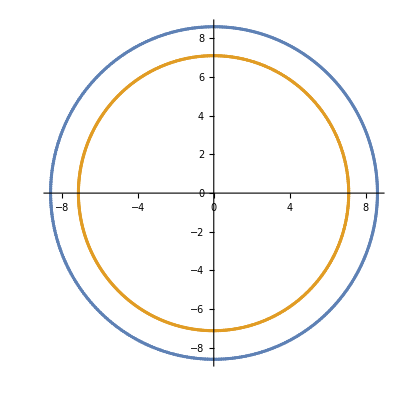

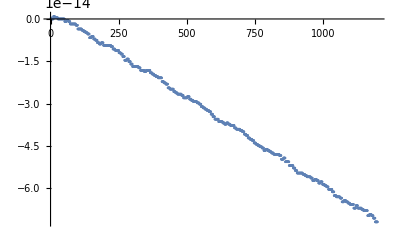

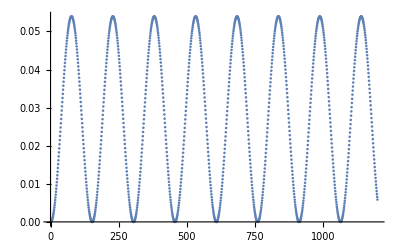

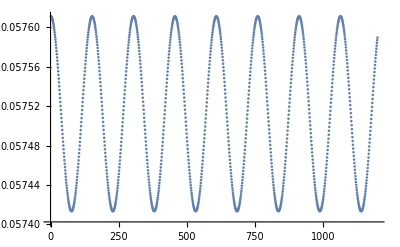

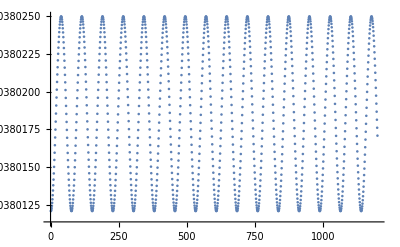

```mathematica
ListPlot[{Transpose[{x1,y1}],Transpose[{x2,y2}]},AspectRatio->1]
ListPlot[hamil]
ListPlot[dist]
ListPlot[lin1]
ListPlot[ang1]
```